# UniDyn--Demo-05.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  Use the UniDyn Evolver function to calculate the evolution of the magnetization of a two coupled spin = 1/2 particles under COSY pulse sequence.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$PackagePath ="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$PackagePath];
FindFile["UniDyn`"]
```

/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/UniDyn/UniDyn.m

Now that we are confident that the path is set correctlly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =False;
Needs["UniDyn`"]
```

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

NCMultiplication.m loaded

NC1SetCommands.m loaded

NCInverses.m loaded

NCTransposes.m loaded

NCAdjoints.m loaded

NCCo.m loaded

NCRoots.m loaded

NC2SetCommands.m loaded

NCCollect.m loaded

NCSubstitute.m loaded

NCMonomial.m loaded

NCSolve.m loaded

NCTools.m loaded

NC2SimplifyRational.m loaded

NC1SimplifyRational.m loaded

NCSimplifyRational.m loaded

NCComplex.m loaded

NCMatMult.m loaded

NCDiff.m loaded

NCSchur.m loaded

NCAlias.m loaded

Grabs.m loaded

NCTaylorCoeff.m loaded

NCConvexity.m and NCGuts.m loaded

NCRealizationFunctions.m loaded

NCTeXForm.m loaded

NCTeX::Using 'open' as PDFViewer.

NCTeX.m loaded

NCMaster.m loaded

NCOutput.m loaded

------------------------------------------------------------
NCAlgebra - Version 4.0.6
Compatible with Mathematica Version 9

Authors:
  J. William Helton*
  Mauricio de Oliveira* 
  Mark Stankus* 
  Robert L. Miller#

* Math Dept, UCSD                
# General Atomics Corp
  La  Jolla, CA 92093

Copyright: 
  Helton and Miller June 1991
  Helton 2002
  All rights reserved.

The program was written by the authors and by:
  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,
  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,
  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 
  The beginnings of the program come from eran@slac.
  Considerable recent help came from Igor Klep.


This program was written with support from 
  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,
  UCSD Faculty Mentor Program,
  and US Department of Education.
  Primary support in 2010 is from the 
    NSF Division of Mathematical Sciences.

If you 
  (1) are a user, 
  (2) want to be a user, 
  (3) refer to NCAlgebra in a publication, or 
  (4) have had an interesting experience with NCAlgebra,
let us know by sending an e-mail message to  

  ncalg@math.ucsd.edu. 

We do not want to restrict access to NCAlgebra, but do 
  want to keep track of how it is being used.

For NCAlgebra updates see the web page:

  www.math.ucsd.edu/~ncalg 
------------------------------------------------------------

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

## Evolver with simplification; pulses

Free evolution

```mathematica
SimplifyingEvolver[H_,t_,ρ$0_]:=  

(* H = Hamiltonian operator *)
(* t = time varaible *)
(* ρ$0 = initial density operator *)

	Evolver[H, t, ρ$0]//Simplify// ExpToTrig // FullSimplify
```

Deliver a pulse to the I and S spins.  The Pulse operators distrubute over plus, times, and noncommutative multiply.  Scalars in front of operators can be pulled out front.

```mathematica
Clear[PulseI];
PulseI[ρ$0_Plus,ϕ_,θ_] :=Plus @@ (PulseI[#,ϕ,θ]&) /@ List @@ ρ$0
PulseI[ρ$0_Times,ϕ_,θ_] :=Times@@ (PulseI[#,ϕ,θ]&) /@ List @@ ρ$0
PulseI[ρ$0_NonCommutativeMultiply,ϕ_,θ_] :=NonCommutativeMultiply @@ (PulseI[#,ϕ,θ]&) /@ List @@ ρ$0
PulseI[Times[a_?CommutativeQ,ρ$0_],ϕ_,θ_] := a PulseI[ρ$0,ϕ,θ]
```

```mathematica
PulseI[ρ$0_,ϕ_,θ_] := 

(* ρ$0 = initial density operator *)
(* ϕ = pulse phase *)
(* θ = pulse angle *)

ρ$0 // SimplifyingEvolver[ ω$I (Cos[ϕ] Ix + Sin[ϕ] Iy),t, #]& /. {t-> θ/ω$I}
```

```mathematica
Clear[PulseS];
PulseS[ρ$0_Plus,ϕ_,θ_] :=Plus @@ (PulseS[#,ϕ,θ]&) /@ List @@ ρ$0
PulseS[ρ$0_Times,ϕ_,θ_] :=Times@@ (PulseS[#,ϕ,θ]&) /@ List @@ ρ$0
PulseS[ρ$0_NonCommutativeMultiply,ϕ_,θ_] :=NonCommutativeMultiply @@ (PulseS[#,ϕ,θ]&) /@ List @@ ρ$0
PulseS[Times[a_?CommutativeQ,ρ$0_],ϕ_,θ_] := a PulseS[ρ$0,ϕ,θ]
```

```mathematica
PulseS[ρ$0_,ϕ_,θ_] := 

(* ρ$0 = initial density operator *)
(* ϕ = pulse phase *)
(* θ = pulse angle *)

ρ$0 // SimplifyingEvolver[ ω$S (Cos[ϕ] Sx + Sin[ϕ] Sy),t, #]& /. {t-> θ/ω$S}
```

## Unitary evolution of two coupled spins

### Create a two spins

The assumptions define below are required for Mathematica to recognize √(–Δ^2-ω^2)= I √(Δ^2+ω^2) inside an exponential.   One of the variables has to be defined to be > 0 and not just ⩾ 0.

```mathematica
Clear[

Δ$I,                 (* Resonance offset frequency *)
Δ$S,                 (* Resonance offset frequency *)
J,                      (* Spin-spin coupling *)
Ix, Iy, Iz, (* Spin angular momentum operators *)
Sx, Sy, Sz, (* Spin angular momentum operators *)
ρ,                      (* Spin density operator *) 
t,                       (* Time *)
t1,                     (* Time *)
t2,                     (* Time *)
a,                        (* Curie Law factor *)
b,                       (* Curie Law factor *)
ρ$0,                  (* Initial spin density operator *)
H                          (* Spin Hamiltonian *)]

CreateScalar[Δ$I,Δ$S,J,t,t1,t2,a,b ];
CreateOperator[{{Ix, Iy, Iz},{Sx, Sy, Sz}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, L=1/2];
SpinSingle$CreateOperators[Sx, Sy, Sz, L=1/2];

$Assumptions  = {Element[Δ$I, Reals], Δ$I ⩾ 0, Element[Δ$S, Reals], Δ$S ⩾ 0, Element[J, Reals], J  > 0};
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

### Spin Hamiltonian

```mathematica
Clear[FreeEvolution];
FreeEvolution[ρ_Plus,t_] :=Plus @@ (FreeEvolution[#,t]&) /@ List @@ ρ
FreeEvolution[ρ_Times,t_] :=Times@@ (FreeEvolution[#,t]&) /@ List @@ ρ
FreeEvolution[ρ_NonCommutativeMultiply,t_] :=NonCommutativeMultiply @@ (FreeEvolution[#,t]&) /@ List @@ ρ
FreeEvolution[Times[a_?CommutativeQ,ρ_],t_] := a FreeEvolution[ρ,t]
```

```mathematica
FreeEvolution[ρ_,t_] := ρ // SimplifyingEvolver[Δ$I Iz,t, #]& // SimplifyingEvolver[ Δ$S Sz,t, #]& // SimplifyingEvolver[ J Iz**Sz,t, #]&
```

### Test pulses

```mathematica
PulseI[Iz+ Cos[t1] Sx**Iz,0,π]  // FullForm
PulseI[Iz+ Cos[t1] Sx**Iz + Cos[t2] Sy**Iy,0,π/2] // FullForm
```

Plus[Times[-1,Iz],Times[-1,Cos[t1],NonCommutativeMultiply[Sx,Iz]]]

Plus[Times[-1,Iy],Times[-1,Cos[t1],NonCommutativeMultiply[Sx,Iy]],Times[Cos[t2],NonCommutativeMultiply[Sy,Iz]]]

```mathematica
PulseI[Iz+ Cos[t1] Sx**Iz + Cos[t2] Sy**Iy,0,π/2]
```

-Iy-Cos[t1] Sx**Iy+Cos[t2] Sy**Iz

## Load Spin 1/2 matrices

```mathematica
<<Matrices--two-spin-half.m
```

Loaded spin one-half matrices for mIx, mIy, mIz, mSx, mSy, mSz

This set of rules will substitute appropriate 4 x 4 matrices for the symbolic spin operators above.

```mathematica
SubstituteSpinMatrices = {Ix-> mIx,Iy-> mIy,Iz-> mIz,Sx-> mSx,Sy-> mSy,Sz-> mSz} ;
```

## Utility Functions

Array of time data

```mathematica
TimeArray[NN_,T_] := 

(* NN = number of points      *)
(* T = total acquisition time *)

Module[{dt,t},
dt = T/(NN-1);
t = Table[ii*dt,{ii,0,NN-1}];
Return[t]]
```

Check out the time step and Nyquist frequency

```mathematica
TimeArrayReport[t_]:=

(* t = List of time points *)

Module[{dt},
dt = t[[2]] - t[[1]];
Print["The time step is ",dt," s"];
Print["The Nyquist frequency is ",1/(2*dt)," Hz"]]
```

A function to calculate the digital Fourier transform of signal.

```mathematica
DFFT[signal_,t_, query_:True] :=

 (* signal = A function that computes the signal *)
 (* t = List of time points *)
 (* query = True or False *)    
 (*    True to plot both real and imaginary FT parts *)

Module[{NN},

NN = Dimensions[signal /@ t][[1]];
FFTS = RotateRight[Fourier[signal/@ t],NN/2];

T = t[[-1]];
f = Table[jj/T,{jj,-NN/2,NN/2-1}];

p1= ListLinePlot[
{Transpose[{t,Re[signal /@ t]}],
Transpose[{t,Im[signal/@ t]}]},
PlotRange->{-1,1},
AxesLabel-> {"time [s]","signal"}];

If[query == True,

p2=ListLinePlot[
{Transpose[{f,Re[FFTS]}],
Transpose[{f,Im[FFTS]}] },
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}],

p2=ListLinePlot[
Transpose[{f,Re[FFTS]}],
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}]
];

Show[GraphicsGrid[{{p1,p2}}]]
]
```

## Calculate Free Evolution

Edit the chemical shifts and the J-couplings here

```mathematica
HamiltonianParameters$coupled =  {Δ$I-> 2π * 100,Δ$S -> 2π *300, J ->2π * 50,T2 -> 0.2};
```

```mathematica
HamiltonianParameters$uncoupled =  {Δ$I-> 2π * 100,Δ$S -> 2π *300, J ->0, T2 -> 0.2};
```

```mathematica
ρ = FreeEvolution[Ix + Sx,t] Exp[-t/T2]
```

ⅇ^(-t/T2) (Cos[(J t)/2] (Ix Cos[t Δ$I]+Iy Sin[t Δ$I])+2 Sin[(J t)/2] (Cos[t Δ$I] Iy**Sz-Ix**Sz Sin[t Δ$I])+Cos[(J t)/2] (Sx Cos[t Δ$S]+Sy Sin[t Δ$S])+2 Sin[(J t)/2] (Cos[t Δ$S] Iz**Sy-Iz**Sx Sin[t Δ$S]))

```mathematica
Signal[t_] = Tr[ρ . ((Ix + Sx) + I (Iy + Sy)) ] /.  SubstituteSpinMatrices /. HamiltonianParameters$coupled
```

2 ⅇ^(-5. t) Cos[50 π t] (1/2 Cos[200 π t]+1/2 ⅈ Sin[200 π t])+2 ⅇ^(-5. t) Cos[50 π t] (1/2 Cos[600 π t]+1/2 ⅈ Sin[600 π t])

```mathematica
t$List = TimeArray[2^10,1.0];
t$List  // TimeArrayReport
```

The time step is 0.000977517 s

The Nyquist frequency is 511.5 Hz

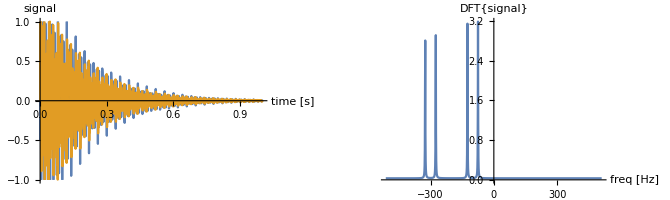

```mathematica
DFFT[Signal,t$List,False]
```

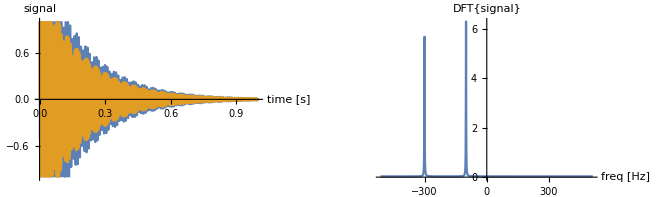

```mathematica
ρ = FreeEvolution[(Ix+Sx) ,t] Exp[-t/T2];
Signal[t_] = Tr[ρ . ((Ix + Sx) + I (Iy + Sy)) ] /.  SubstituteSpinMatrices /. HamiltonianParameters$uncoupled;
DFFT[Signal,t$List,False]
```

ⅇ^(-t/T2) (Cos[(J t)/2] (Ix Cos[t Δ$I]+Iy Sin[t Δ$I])+2 Sin[(J t)/2] (Cos[t Δ$I] Iy**Sz-Ix**Sz Sin[t Δ$I]))

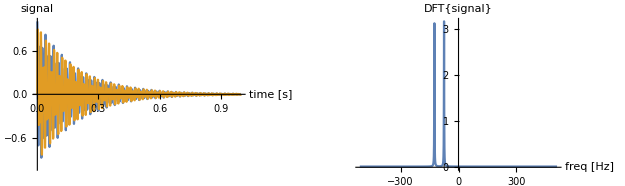

```mathematica
ρ = FreeEvolution[Ix ,t] Exp[-t/T2]
Signal[t_] = Tr[ρ . ((Ix + Sx) + I (Iy + Sy)) ] /.  SubstituteSpinMatrices /. HamiltonianParameters$coupled;
DFFT[Signal,t$List,False]
```

ⅇ^(-t/T2) (Cos[(J t)/2] (Sx Cos[t Δ$S]+Sy Sin[t Δ$S])+2 Sin[(J t)/2] (Cos[t Δ$S] Iz**Sy-Iz**Sx Sin[t Δ$S]))

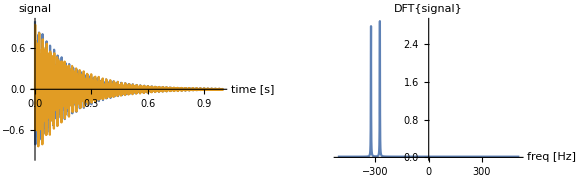

```mathematica
ρ = FreeEvolution[Sx ,t] Exp[-t/T2]
Signal[t_] = Tr[ρ . ((Ix + Sx) + I (Iy + Sy)) ] /.  SubstituteSpinMatrices /. HamiltonianParameters$coupled;
DFFT[Signal,t$List,False]
```

## INEPT Polarization Transfer

```mathematica
ρ$0  = a Iz + b Sz//  PulseS[#,π/2,π/2]&
ρ$1 = (ρ$0 //  FreeEvolution[#,t]&  // NCExpand) /. {Δ$I-> 0,Δ$S-> 0}
```

a Iz+b Sx

a Iz+b Sx Cos[(J t)/2]+2 b Iz**Sy Sin[(J t)/2]

```mathematica
Tr[ρ$1.Sx] /. SubstituteSpinMatrices
```

b Cos[(J t)/2]

```mathematica
ρ$0  = a Iz + b Sz//  PulseI[#,π/2,π/2]&
ρ$1 = (ρ$0 //  FreeEvolution[#,t]&  // NCExpand) /. {Δ$I-> 0}
ρ$2 = ρ$1 //  PulseI[#,0,π]& //  PulseS[#,0,π] &
ρ$3 = (ρ$2 //  FreeEvolution[#,t]&  // NCExpand) /. {Δ$I-> 0} 
ρ$4 = ρ$3 //  PulseI[#,0,π/2]& //  PulseS[#,π/2,π/2] &
```

a Ix+b Sz

b Sz+a Ix Cos[(J t)/2]+2 a Iy**Sz Sin[(J t)/2]

-b Sz+a Ix Cos[(J t)/2]+2 a Iy**Sz Sin[(J t)/2]

-b Sz+a Ix Cos[(J t)/2]^2+4 a Cos[(J t)/2] Iy**Sz Sin[(J t)/2]-a Ix Sin[(J t)/2]^2

-b Sx+a Ix Cos[(J t)/2]^2+4 a Cos[(J t)/2] Iz**Sx Sin[(J t)/2]-a Ix Sin[(J t)/2]^2

```mathematica
ρ$5 = ρ$4  /. {t-> 2 π/(4 J)} // FreeEvolution[#,t]& // NCExpand
```

-b Sx Cos[(J t)/2] Cos[t Δ$S]+2 a Cos[(J t)/2] Cos[t Δ$S] Iz**Sx+a Sy Cos[t Δ$S] Sin[(J t)/2]-2 b Cos[t Δ$S] Iz**Sy Sin[(J t)/2]-b Sy Cos[(J t)/2] Sin[t Δ$S]+2 a Cos[(J t)/2] Iz**Sy Sin[t Δ$S]-a Sx Sin[(J t)/2] Sin[t Δ$S]+2 b Iz**Sx Sin[(J t)/2] Sin[t Δ$S]

```mathematica
Tr[ρ$5.(Sx + I Sy)] /. {Δ$I-> 0,Δ$S-> 0} /. SubstituteSpinMatrices
```

-b Cos[(J t)/2]+ⅈ a Sin[(J t)/2]

## Calculate the COSY signal

```mathematica
ρ$0 = Iz+ Sz;
ρ$1 = ρ$0 // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]&
```

Ix+Sx

```mathematica
ρ$2 = ρ$1 //  FreeEvolution[#,t1]&
```

Cos[(J t1)/2] (Ix Cos[t1 Δ$I]+Iy Sin[t1 Δ$I])+2 Sin[(J t1)/2] (Cos[t1 Δ$I] Iy**Sz-Ix**Sz Sin[t1 Δ$I])+Cos[(J t1)/2] (Sx Cos[t1 Δ$S]+Sy Sin[t1 Δ$S])+2 Sin[(J t1)/2] (Cos[t1 Δ$S] Iz**Sy-Iz**Sx Sin[t1 Δ$S])

```mathematica
ρ$3 = ρ$2  // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]&
```

Cos[(J t1)/2] (-Iz Cos[t1 Δ$I]+Iy Sin[t1 Δ$I])+2 Sin[(J t1)/2] (Cos[t1 Δ$I] Iy**Sx+Iz**Sx Sin[t1 Δ$I])+Cos[(J t1)/2] (-Sz Cos[t1 Δ$S]+Sy Sin[t1 Δ$S])+2 Sin[(J t1)/2] (Cos[t1 Δ$S] Ix**Sy+Ix**Sz Sin[t1 Δ$S])

```mathematica
IxSx$evolved= FreeEvolution[(Ix+Sx) + I (Iy + Sy) ,-t2]
```

Cos[(J t2)/2] (Ix Cos[t2 Δ$I]-Iy Sin[t2 Δ$I])-2 Sin[(J t2)/2] (Cos[t2 Δ$I] Iy**Sz+Ix**Sz Sin[t2 Δ$I])+Cos[(J t2)/2] (Sx Cos[t2 Δ$S]-Sy Sin[t2 Δ$S])-2 Sin[(J t2)/2] (Cos[t2 Δ$S] Iz**Sy+Iz**Sx Sin[t2 Δ$S])+ⅈ (Cos[(J t2)/2] (Iy Cos[t2 Δ$I]+Ix Sin[t2 Δ$I])+2 Sin[(J t2)/2] (Cos[t2 Δ$I] Ix**Sz-Iy**Sz Sin[t2 Δ$I])+Cos[(J t2)/2] (Sy Cos[t2 Δ$S]+Sx Sin[t2 Δ$S])+2 Sin[(J t2)/2] (Cos[t2 Δ$S] Iz**Sx-Iz**Sy Sin[t2 Δ$S]))

```mathematica
Signal2D[t1_,t2_] = Tr[ρ$3**IxSx$evolved] Exp[-t1/T2] Exp[-t2/T2] //ExpandAll// NCExpand  // MultSort
```

ⅇ^(-t1/T2-t2/T2) Tr[-Cos[(J t1)/2] Cos[t1 Δ$I] (1/2 Ix Cos[(J t2)/2] Cos[t2 Δ$I]+1/2 ⅈ Iy Cos[(J t2)/2] Cos[t2 Δ$I]+Cos[(J t2)/2] Cos[t2 Δ$S] Iz**Sx+ⅈ Cos[(J t2)/2] Cos[t2 Δ$S] Iz**Sy+1/2 ⅈ Sx Cos[t2 Δ$S] Sin[(J t2)/2]-1/2 Sy Cos[t2 Δ$S] Sin[(J t2)/2]+ⅈ Cos[t2 Δ$I] Ix**Sz Sin[(J t2)/2]-Cos[t2 Δ$I] Iy**Sz Sin[(J t2)/2]+1/2 ⅈ Ix Cos[(J t2)/2] Sin[t2 Δ$I]-1/2 Iy Cos[(J t2)/2] Sin[t2 Δ$I]-Ix**Sz Sin[(J t2)/2] Sin[t2 Δ$I]-ⅈ Iy**Sz Sin[(J t2)/2] Sin[t2 Δ$I]+ⅈ Cos[(J t2)/2] Iz**Sx Sin[t2 Δ$S]-Cos[(J t2)/2] Iz**Sy Sin[t2 Δ$S]-1/2 Sx Sin[(J t2)/2] Sin[t2 Δ$S]-1/2 ⅈ Sy Sin[(J t2)/2] Sin[t2 Δ$S])+2 Sin[(J t1)/2] Sin[t1 Δ$I] (1/4 Iz Cos[(J t2)/2] Cos[t2 Δ$S]+1/2 Cos[(J t2)/2] Cos[t2 Δ$I] Ix**Sx+1/2 ⅈ Cos[(J t2)/2] Cos[t2 Δ$I] Iy**Sx-1/2 Cos[(J t2)/2] Cos[t2 Δ$S] Iz**Sz+1/8 ⅈ Cos[t2 Δ$S] Sin[(J t2)/2]-1/4 ⅈ Sz Cos[t2 Δ$S] Sin[(J t2)/2]+1/2 Cos[t2 Δ$I] Ix**Sy Sin[(J t2)/2]+1/2 ⅈ Cos[t2 Δ$I] Iy**Sy Sin[(J t2)/2]+1/2 ⅈ Cos[(J t2)/2] Ix**Sx Sin[t2 Δ$I]-1/2 Cos[(J t2)/2] Iy**Sx Sin[t2 Δ$I]+1/2 ⅈ Ix**Sy Sin[(J t2)/2] Sin[t2 Δ$I]-1/2 Iy**Sy Sin[(J t2)/2] Sin[t2 Δ$I]+1/4 ⅈ Iz Cos[(J t2)/2] Sin[t2 Δ$S]-1/2 ⅈ Cos[(J t2)/2] Iz**Sz Sin[t2 Δ$S]-1/8 Sin[(J t2)/2] Sin[t2 Δ$S]+1/4 Sz Sin[(J t2)/2] Sin[t2 Δ$S])+Cos[(J t1)/2] Sin[t1 Δ$I] (1/4 ⅈ Cos[(J t2)/2] Cos[t2 Δ$I]-1/2 ⅈ Iz Cos[(J t2)/2] Cos[t2 Δ$I]+Cos[(J t2)/2] Cos[t2 Δ$S] Iy**Sx+ⅈ Cos[(J t2)/2] Cos[t2 Δ$S] Iy**Sy-1/2 Sz Cos[t2 Δ$I] Sin[(J t2)/2]-Cos[t2 Δ$S] Ix**Sx Sin[(J t2)/2]-ⅈ Cos[t2 Δ$S] Ix**Sy Sin[(J t2)/2]+Cos[t2 Δ$I] Iz**Sz Sin[(J t2)/2]-1/4 Cos[(J t2)/2] Sin[t2 Δ$I]+1/2 Iz Cos[(J t2)/2] Sin[t2 Δ$I]-1/2 ⅈ Sz Sin[(J t2)/2] Sin[t2 Δ$I]+ⅈ Iz**Sz Sin[(J t2)/2] Sin[t2 Δ$I]+ⅈ Cos[(J t2)/2] Iy**Sx Sin[t2 Δ$S]-Cos[(J t2)/2] Iy**Sy Sin[t2 Δ$S]-ⅈ Ix**Sx Sin[(J t2)/2] Sin[t2 Δ$S]+Ix**Sy Sin[(J t2)/2] Sin[t2 Δ$S])+2 Cos[t1 Δ$I] Sin[(J t1)/2] (1/4 ⅈ Sx Cos[(J t2)/2] Cos[t2 Δ$I]+1/4 Iy Cos[(J t2)/2] Cos[t2 Δ$S]-1/2 Cos[(J t2)/2] Cos[t2 Δ$S] Iy**Sz-1/2 ⅈ Cos[(J t2)/2] Cos[t2 Δ$I] Iz**Sx+1/4 ⅈ Sy Cos[t2 Δ$I] Sin[(J t2)/2]-1/4 Ix Cos[t2 Δ$S] Sin[(J t2)/2]+1/2 Cos[t2 Δ$S] Ix**Sz Sin[(J t2)/2]-1/2 ⅈ Cos[t2 Δ$I] Iz**Sy Sin[(J t2)/2]-1/4 Sx Cos[(J t2)/2] Sin[t2 Δ$I]+1/2 Cos[(J t2)/2] Iz**Sx Sin[t2 Δ$I]-1/4 Sy Sin[(J t2)/2] Sin[t2 Δ$I]+1/2 Iz**Sy Sin[(J t2)/2] Sin[t2 Δ$I]+1/4 ⅈ Iy Cos[(J t2)/2] Sin[t2 Δ$S]-1/2 ⅈ Cos[(J t2)/2] Iy**Sz Sin[t2 Δ$S]-1/4 ⅈ Ix Sin[(J t2)/2] Sin[t2 Δ$S]+1/2 ⅈ Ix**Sz Sin[(J t2)/2] Sin[t2 Δ$S])+2 Sin[(J t1)/2] Sin[t1 Δ$S] (1/4 Sz Cos[(J t2)/2] Cos[t2 Δ$I]+1/2 Cos[(J t2)/2] Cos[t2 Δ$S] Ix**Sx+1/2 ⅈ Cos[(J t2)/2] Cos[t2 Δ$S] Ix**Sy-1/2 Cos[(J t2)/2] Cos[t2 Δ$I] Iz**Sz+1/8 ⅈ Cos[t2 Δ$I] Sin[(J t2)/2]-1/4 ⅈ Iz Cos[t2 Δ$I] Sin[(J t2)/2]+1/2 Cos[t2 Δ$S] Iy**Sx Sin[(J t2)/2]+1/2 ⅈ Cos[t2 Δ$S] Iy**Sy Sin[(J t2)/2]+1/4 ⅈ Sz Cos[(J t2)/2] Sin[t2 Δ$I]-1/2 ⅈ Cos[(J t2)/2] Iz**Sz Sin[t2 Δ$I]-1/8 Sin[(J t2)/2] Sin[t2 Δ$I]+1/4 Iz Sin[(J t2)/2] Sin[t2 Δ$I]+1/2 ⅈ Cos[(J t2)/2] Ix**Sx Sin[t2 Δ$S]-1/2 Cos[(J t2)/2] Ix**Sy Sin[t2 Δ$S]+1/2 ⅈ Iy**Sx Sin[(J t2)/2] Sin[t2 Δ$S]-1/2 Iy**Sy Sin[(J t2)/2] Sin[t2 Δ$S])+2 Cos[t1 Δ$S] Sin[(J t1)/2] (1/4 Sy Cos[(J t2)/2] Cos[t2 Δ$I]+1/4 ⅈ Ix Cos[(J t2)/2] Cos[t2 Δ$S]-1/2 ⅈ Cos[(J t2)/2] Cos[t2 Δ$S] Ix**Sz-1/2 Cos[(J t2)/2] Cos[t2 Δ$I] Iz**Sy-1/4 Sx Cos[t2 Δ$I] Sin[(J t2)/2]+1/4 ⅈ Iy Cos[t2 Δ$S] Sin[(J t2)/2]-1/2 ⅈ Cos[t2 Δ$S] Iy**Sz Sin[(J t2)/2]+1/2 Cos[t2 Δ$I] Iz**Sx Sin[(J t2)/2]+1/4 ⅈ Sy Cos[(J t2)/2] Sin[t2 Δ$I]-1/2 ⅈ Cos[(J t2)/2] Iz**Sy Sin[t2 Δ$I]-1/4 ⅈ Sx Sin[(J t2)/2] Sin[t2 Δ$I]+1/2 ⅈ Iz**Sx Sin[(J t2)/2] Sin[t2 Δ$I]-1/4 Ix Cos[(J t2)/2] Sin[t2 Δ$S]+1/2 Cos[(J t2)/2] Ix**Sz Sin[t2 Δ$S]-1/4 Iy Sin[(J t2)/2] Sin[t2 Δ$S]+1/2 Iy**Sz Sin[(J t2)/2] Sin[t2 Δ$S])-Cos[(J t1)/2] Cos[t1 Δ$S] (1/2 Sx Cos[(J t2)/2] Cos[t2 Δ$S]+1/2 ⅈ Sy Cos[(J t2)/2] Cos[t2 Δ$S]+Cos[(J t2)/2] Cos[t2 Δ$I] Ix**Sz+ⅈ Cos[(J t2)/2] Cos[t2 Δ$I] Iy**Sz+1/2 ⅈ Ix Cos[t2 Δ$I] Sin[(J t2)/2]-1/2 Iy Cos[t2 Δ$I] Sin[(J t2)/2]+ⅈ Cos[t2 Δ$S] Iz**Sx Sin[(J t2)/2]-Cos[t2 Δ$S] Iz**Sy Sin[(J t2)/2]+ⅈ Cos[(J t2)/2] Ix**Sz Sin[t2 Δ$I]-Cos[(J t2)/2] Iy**Sz Sin[t2 Δ$I]-1/2 Ix Sin[(J t2)/2] Sin[t2 Δ$I]-1/2 ⅈ Iy Sin[(J t2)/2] Sin[t2 Δ$I]+1/2 ⅈ Sx Cos[(J t2)/2] Sin[t2 Δ$S]-1/2 Sy Cos[(J t2)/2] Sin[t2 Δ$S]-Iz**Sx Sin[(J t2)/2] Sin[t2 Δ$S]-ⅈ Iz**Sy Sin[(J t2)/2] Sin[t2 Δ$S])+Cos[(J t1)/2] Sin[t1 Δ$S] (1/4 ⅈ Cos[(J t2)/2] Cos[t2 Δ$S]-1/2 ⅈ Sz Cos[(J t2)/2] Cos[t2 Δ$S]+Cos[(J t2)/2] Cos[t2 Δ$I] Ix**Sy+ⅈ Cos[(J t2)/2] Cos[t2 Δ$I] Iy**Sy-1/2 Iz Cos[t2 Δ$S] Sin[(J t2)/2]-Cos[t2 Δ$I] Ix**Sx Sin[(J t2)/2]-ⅈ Cos[t2 Δ$I] Iy**Sx Sin[(J t2)/2]+Cos[t2 Δ$S] Iz**Sz Sin[(J t2)/2]+ⅈ Cos[(J t2)/2] Ix**Sy Sin[t2 Δ$I]-Cos[(J t2)/2] Iy**Sy Sin[t2 Δ$I]-ⅈ Ix**Sx Sin[(J t2)/2] Sin[t2 Δ$I]+Iy**Sx Sin[(J t2)/2] Sin[t2 Δ$I]-1/4 Cos[(J t2)/2] Sin[t2 Δ$S]+1/2 Sz Cos[(J t2)/2] Sin[t2 Δ$S]-1/2 ⅈ Iz Sin[(J t2)/2] Sin[t2 Δ$S]+ⅈ Iz**Sz Sin[(J t2)/2] Sin[t2 Δ$S])]

```mathematica
COSY[t1_,t2_] = Signal2D[t1,t2]/.  SubstituteSpinMatrices /. HamiltonianParameters$coupled // Simplify
```

ⅈ ⅇ^(-5. t1-5. t2) (Sin[50 π t1] Sin[50 π t2] (Cos[600 π t2] Sin[200 π t1]+Cos[200 π t2] Sin[600 π t1]+ⅈ (Sin[600 π t1] Sin[200 π t2]+Sin[200 π t1] Sin[600 π t2]))+Cos[50 π t1] Cos[50 π t2] (Cos[200 π t2] Sin[200 π t1]+Cos[600 π t2] Sin[600 π t1]+ⅈ (Sin[200 π t1] Sin[200 π t2]+Sin[600 π t1] Sin[600 π t2])))

Edit the digitization rates and acquitisition times here.

```mathematica
f$1$dig = 800;
t$1$acq = (128-1)/f$1$dig;

f$2$dig = 800;
t$2$acq = (128-1)/f$2$dig;
```

This may take many seconds to evaluate.  It's a big matrix of data.

```mathematica
COSY$data = Table[COSY[t1,t2],{t2,0,t$2$acq,1/f$2$dig},{t1,0,t$1$acq,1/f$1$dig}];

t1$axis = Table[t1,{t1,0,t$1$acq,1/f$1$dig}];
t2$axis = Table[t1,{t2,0,t$2$acq,1/f$2$dig}];
```

Calculate the number of points in each time dimension

```mathematica
t1$n = Dimensions[t1$axis][[1]];
t2$n = Dimensions[t2$axis][[1]];
{t1$n,t2$n}
```

{128,128}

Carry out a two-dimensonal Fourier transform.  Just as when we Fourier transformed the FID above, we have to RotateLeft the data to get the zero frequency in the middle of the spectrum (now a two-dimensional spectrum).

```mathematica
COSY$FT$data = RotateLeft[Fourier[COSY$data],{t2$n/2,t1$n/2}];

ω1$axis= Table[ω1,{ω1,-f$1$dig/2,f$1$dig,1/t$1$acq}]; 
ω2$axis= Table[ω2,{ω2,-f$2$dig/2,f$2$dig,1/t$2$acq}];
```

```mathematica
SetOptions[ListPlot3D,PlotRange->All,DataRange->{{ω1$axis⟦1⟧,ω1$axis⟦t1$n⟧},{ω2$axis⟦1⟧,ω2$axis⟦t2$n⟧}},PlotLabel->"COSY spectrum for two J-couple protons\n\n",Mesh->False];

ListPlot3D[Re[COSY$FT$data],AxesLabel->{"ω1 [Hz]","ω2 [Hz]","Re[FT[COSY(t1,t2)]]"},ViewPoint->{1.561,-2.881,0.845}]

ListPlot3D[Im[COSY$FT$data],AxesLabel->{"ω1 [Hz]","ω2 [Hz]","Im[FT[COSY(t1,t2)]]"},ViewPoint->{1.561,-2.881,0.845}]

ListPlot3D[Abs[COSY$FT$data],AxesLabel->{"ω1 [Hz]","ω2 [Hz]","Abs[FT[COSY(t1,t2)]]"},ViewPoint->{1.561,-2.881,0.845}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## Scratch

```mathematica
IzOp[1/2] = {{1/2,0},{0,-1/2}};
IzOp[1/2]  // MatrixForm
```

(1/2 | 0
0 | -1/2)

```mathematica
IdOp[1/2]= IdentityMatrix[2];
IdOp[1/2] // MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Az = Outer[Times,IzOp[1/2] ,IdOp[1/2] ] // ArrayFlatten;
Bz = Outer[Times,IdOp[1/2]  ,IzOp[1/2]]  // ArrayFlatten;
```

```mathematica
Az // MatrixForm
Bz // MatrixForm
```

(1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -1/2)

(1/2 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | -1/2)

```mathematica
Az.Az // MatrixForm
Bz.Bz // MatrixForm
```

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4)

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/4)